```mathematica
omega = 2000*2*Pi;
rin= 12000;
rout=6800;
c1=.1*10^-6;
c2 = .1*10^-6;
ampgain = 30;
outputgain  = omega*rout*c2/(Sqrt[1+(omega*rout*c2)^2])
inputgain = omega*rin*c2/(Sqrt[1+(omega*rin*c1)^2])
totalgain = outputgain*inputgain* ampgain
```

0.993222

0.997808

29.7314

```mathematica
21/.6
```

35.

```mathematica
.3/.0216
```

13.8889

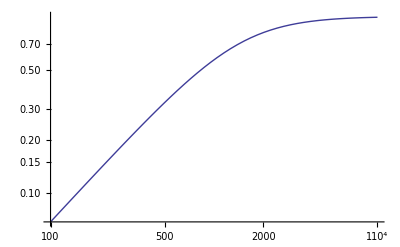

```mathematica
c7 = .22*10^-6;
r8=1000;
r9=1000;
omega = 100*2 *Pi;
rboth=1/(1/r8+1/r9);
LogLogPlot[x*2*Pi*rboth*c7/(Sqrt[1+(x*2*Pi*rboth*c7)^2]),{x,100,10000}]
```

```mathematica
Clear[r17,r18,r19,r20];
r17=1000;
r18 = 47000;
Solve[{2==(r20/(r18+r19+r20))*15.,1== r20*(15+r18/r17*.5)/(r18+r19+r20+r18*r20/r17)},{r19,r20}]
r19 = 4700;
r20 = 4700;

VOn=(r20/(r18+r19+r20))*15.
VOff = r20*(15+r18/r17*.5)/(r18+r19+r20+r18*r20/r17)
```

{}

1.25

0.652542